## G2 roots

```mathematica
G2Roots=;
```

## F4 roots

```mathematica
F4Roots=;
```

## E8 roots

```mathematica
E8Roots=Join[
Union@@(Permutations[Join[#,ConstantArray[0,6]]]&/@Tuples[{-1,1},2]),
Select[Tuples[{1/2,-1/2},8],EvenQ@*Total]];
```

## SO (n)

Get roots from generators

```mathematica
SORoots[n_]:=Block[
{ϕ},
With[{generators=D[#,ϕ]/.ϕ->0&/@SO[n]},
generatorsToRoots[generators]["roots"]
]
]
```

Guess formulas as following (personally guess and verify till n = 14)

```mathematica
SORoots[2]:={{1}};
SORoots[n_/;n>=4&&EvenQ[n]]:=Catenate[Permutations[PadRight[#,n/2]]&/@{{1,1},{-1,1},{-1,-1}}]

SORoots[3]:={{1},{-1}};
SORoots[n_/;n>=5&&OddQ[n]]:=Join[SORoots[n-1],IdentityMatrix[(n-1)/2],-IdentityMatrix[(n-1)/2]]
```

Verification to 10

```mathematica
Function[n,
Sort[Block[
{ϕ},
With[{generators=D[#,ϕ]/.ϕ->0&/@SO[n]},
generatorsToRoots[generators]["roots"]
]
]]==Sort[SORoots[n]]
]/@Range[2,10]
```

{True,True,True,True,True,True,True,True,True}

Verify dimensions of SO(n) groups:

```mathematica
Function[n,Length[SO[n]]==(n(n-1)/2)]/@Range[2,20]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

## SU (n)

```mathematica
SURoots[n_/;n>=2]:=Permutations[PadRight[{1,-1},n]]
```

## Roots Graph

```mathematica
generateRootSystem[simpleRoots_]:=Module[{
R,h=Length[simpleRoots]
},
R=IdentityMatrix[Length[First[simpleRoots]]]-2*TensorProduct[#,#]/(#.#)&/@simpleRoots;
FixedPoint[Union@@Transpose[#.Transpose[R]]&,simpleRoots]
]
```

```mathematica
rootsGraph[roots_?MatrixQ]:=Module[{
basis,
rrForm,
coefficients,
positiveRoots,
simpleRoots,
R,coxeter,
U,
vertexStyles,
vertexCoordinates,
edges,g,
h
},
rrForm=RowReduce[Transpose[roots]];
basis=roots[[Catenate[FirstPosition[1]/@rrForm]]];
coefficients=Transpose[rrForm[[;;Length[basis]]]];
positiveRoots=Pick[roots,Positive@*SelectFirst[#!=0&]/@coefficients,True];
simpleRoots=Complement[positiveRoots,Plus@@@Subsets[positiveRoots,{2}]];

R = Function[IdentityMatrix[Length[First[simpleRoots]]]-2*TensorProduct[#,#]/(#.#)]/@simpleRoots;

h = Length[roots] / Length[simpleRoots];

coxeter=Dot@@R;

U=SelectFirst[Eigenvectors[coxeter],Chop[Norm[N[coxeter.#-Exp[2Pi I /h]#]]]==0&];

(*edges=UndirectedEdge@@@Select[Subsets[roots,{2}],MemberQ[{0,Pi/6,Pi/3,Pi/4},VectorAngle@@#]&];*)

With[{
minDistance=Min[Norm[Subtract@@#]&/@Subsets[roots,{2}]]
},
edges=UndirectedEdge@@@Select[Subsets[roots,{2}],Norm[Subtract@@#]==minDistance&];
];

vertexStyles=If[
Head[U]=!=Missing,
Catenate@With[{
groupByNorm=KeySortBy[Norm@*N][
GroupBy[Function[Norm[N[U.#]]]][roots]
]
},
MapIndexed[
Function[#1->Lighter[Hue[First[#2-1]/Length[groupByNorm]],.3]],
Values[groupByNorm],
{2}
]
],
Automatic
];

vertexCoordinates=If[
Head[U]=!=Missing,
Map[Function[ReIm[U.#]],roots],
Automatic
];

g=Graph[
roots,
edges,
VertexCoordinates->vertexCoordinates,
VertexStyle->vertexStyles,
EdgeStyle->Directive[Lighter[Gray,.4],Thin],
ImageSize->900,
Background->Black,
ImageMargins->{{350,350},{0,0}}
]

]
```

## Main Test

```mathematica
g=rootsGraph[generateRootSystem[F4Roots]];
```

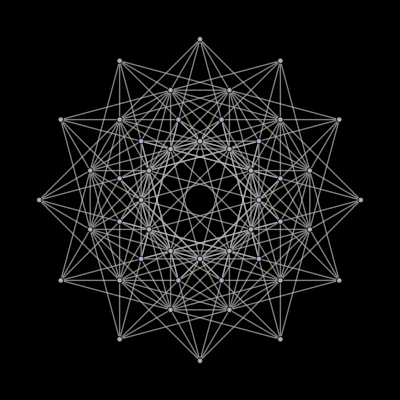
-Graphics-vertex number: 48

```mathematica
Labeled[
Show[g,ImageSize->400,ImageMargins->0],
"vertex number: "<>ToString[VertexCount[g]],
Top
]
```

## Auto Export

```mathematica
Function[n,
Block[{
groupName="SU"<>ToString[n],
g=rootsGraph[SURoots[n]]
},
Export[NotebookDirectory[]<>"figures/"<>groupName<>"-projection.pdf",g]
]
]/@Range[2,16];
```

```mathematica
Function[n,
Block[{
groupName="SO"<>ToString[n],
g=rootsGraph[SORoots[n]]
},
Export[NotebookDirectory[]<>"figures/"<>groupName<>"-projection.pdf",g]
]
]/@Range[2,16];
```